```mathematica
$PlotTheme="Scientific"
```

Scientific

```mathematica
SetOptions[{Plot,ListPlot,ArrayPlot,ContourPlot,DiscretePlot3D},BaseStyle->{14,Directive[FontFamily->"cmr10"]}];
```

# All intertwiners Immirzi 0.1

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
getfile[Dl_,K_]:=  StringJoin["../data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_",ToString[Dl],"/goat_pcutoff_",ToString[NumberForm[N[K],{3,1}]],".csv"];
```

```mathematica
getfile[0,1/2]
```

../data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_0/goat_pcutoff_0.5.csv

```mathematica
NumberForm[N[2],{3,1}]
```

2.0

```mathematica
A00KDl0 = {};
A01KDl0 = {};
A11KDl0 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[0,k],"Data",HeaderLines->1];
AppendTo[A00KDl0,{k,tmp00}];
AppendTo[A01KDl0,{k,tmp01}];
AppendTo[A11KDl0,{k,tmp11}];
]
```

```mathematica
A00KDl1 = {};
A01KDl1 = {};
A11KDl1 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[1,k],"Data",HeaderLines->1];
AppendTo[A00KDl1,{k,tmp00}];
AppendTo[A01KDl1,{k,tmp01}];
AppendTo[A11KDl1,{k,tmp11}];
]
```

```mathematica
A00KDl2 = {};
A01KDl2 = {};
A11KDl2 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[2,k],"Data",HeaderLines->1];
AppendTo[A00KDl2,{k,tmp00}];
AppendTo[A01KDl2,{k,tmp01}];
AppendTo[A11KDl2,{k,tmp11}];
]
```

```mathematica
A00KDl3 = {};
A01KDl3 = {};
A11KDl3 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[3,k],"Data",HeaderLines->1];
AppendTo[A00KDl3,{k,tmp00}];
AppendTo[A01KDl3,{k,tmp01}];
AppendTo[A11KDl3,{k,tmp11}];
]
```

```mathematica
A00KDl4 = {};
A01KDl4 = {};
A11KDl4 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[4,k],"Data",HeaderLines->1];
AppendTo[A00KDl4,{k,tmp00}];
AppendTo[A01KDl4,{k,tmp01}];
AppendTo[A11KDl4,{k,tmp11}];
]
```

```mathematica
A00KDl5 = {};
A01KDl5 = {};
A11KDl5 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[5,k],"Data",HeaderLines->1];
AppendTo[A00KDl5,{k,tmp00}];
AppendTo[A01KDl5,{k,tmp01}];
AppendTo[A11KDl5,{k,tmp11}];
]
```

```mathematica
A00KDl6 = {};
A01KDl6 = {};
A11KDl6 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[6,k],"Data",HeaderLines->1];
AppendTo[A00KDl6,{k,tmp00}];
AppendTo[A01KDl6,{k,tmp01}];
AppendTo[A11KDl6,{k,tmp11}];
]
```

```mathematica
A00KDl7 = {};
A01KDl7 = {};
A11KDl7 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[7,k],"Data",HeaderLines->1];
AppendTo[A00KDl7,{k,tmp00}];
AppendTo[A01KDl7,{k,tmp01}];
AppendTo[A11KDl7,{k,tmp11}];
]
```

```mathematica
A00KDl8 = {};
A01KDl8 = {};
A11KDl8 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[8,k],"Data",HeaderLines->1];
AppendTo[A00KDl8,{k,tmp00}];
AppendTo[A01KDl8,{k,tmp01}];
AppendTo[A11KDl8,{k,tmp11}];
]
```

```mathematica
A00KDl9 = {};
A01KDl9 = {};
A11KDl9 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[9,k],"Data",HeaderLines->1];
AppendTo[A00KDl9,{k,tmp00}];
AppendTo[A01KDl9,{k,tmp01}];
AppendTo[A11KDl9,{k,tmp11}];
]
```

```mathematica
A00KDl10 = {};
A01KDl10 = {};
A11KDl10 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[10,k],"Data",HeaderLines->1];
AppendTo[A00KDl10,{k,tmp00}];
AppendTo[A01KDl10,{k,tmp01}];
AppendTo[A11KDl10,{k,tmp11}];
]
```

```mathematica
Clear[k]
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation00= Aitken/@Transpose[{Last/@A00KDl0,Last/@A00KDl1,Last/@A00KDl2,Last/@A00KDl3,Last/@A00KDl4,Last/@A00KDl5,Last/@A00KDl6,Last/@A00KDl7,Last/@A00KDl8,Last/@A00KDl9,Last/@A00KDl10}]
rExtrapolation01=Aitken/@Transpose[{Last/@A01KDl0,Last/@A01KDl1,Last/@A01KDl2,Last/@A01KDl3,Last/@A01KDl4,Last/@A01KDl5,Last/@A01KDl6,Last/@A01KDl7,Last/@A01KDl8,Last/@A01KDl9,Last/@A01KDl10}]
rExtrapolation11=Aitken/@Transpose[{Last/@A11KDl0,Last/@A11KDl1,Last/@A11KDl2,Last/@A11KDl3,Last/@A11KDl4,Last/@A11KDl5,Last/@A11KDl6,Last/@A11KDl7,Last/@A11KDl8,Last/@A11KDl9,Last/@A11KDl10}]
```

{3.36679×10^-8,3.36717×10^-8,-1.94648×10^-7,-1.87709×10^-7,-1.81972×10^-7,-1.79869×10^-7,-1.78888×10^-7,-1.7836×10^-7,-1.78047×10^-7,-1.77849×10^-7,-1.77717×10^-7,-1.77626×10^-7,-1.77561×10^-7,-1.77513×10^-7,-1.77477×10^-7,-1.7745×10^-7,-1.77428×10^-7,-1.77412×10^-7,-1.77398×10^-7,-1.77387×10^-7,-1.77378×10^-7}

{-1.38462×10^-23,9.16067×10^-9,9.86873×10^-9,3.75252×10^-8,3.47213×10^-8,3.39793×10^-8,3.37333×10^-8,3.36353×10^-8,3.35909×10^-8,3.35686×10^-8,3.35567×10^-8,3.35498×10^-8,3.35457×10^-8,3.35431×10^-8,3.35415×10^-8,3.35403×10^-8,3.35396×10^-8,3.3539×10^-8,3.35387×10^-8,3.35384×10^-8,3.35382×10^-8}

{-3.36235×10^-8,-5.47458×10^-8,1.23231×10^-8,2.63381×10^-8,3.02321×10^-8,3.1243×10^-8,3.15588×10^-8,3.16673×10^-8,3.17048×10^-8,3.17158×10^-8,3.17167×10^-8,3.17138×10^-8,3.17097×10^-8,3.17054×10^-8,3.17015×10^-8,3.16979×10^-8,3.16948×10^-8,3.16922×10^-8,3.16899×10^-8,3.16879×10^-8,3.16862×10^-8}

```mathematica
Extrapolation00=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation00];
Extrapolation01=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation01];
Extrapolation11=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation11];
```

### Intertwiners 00

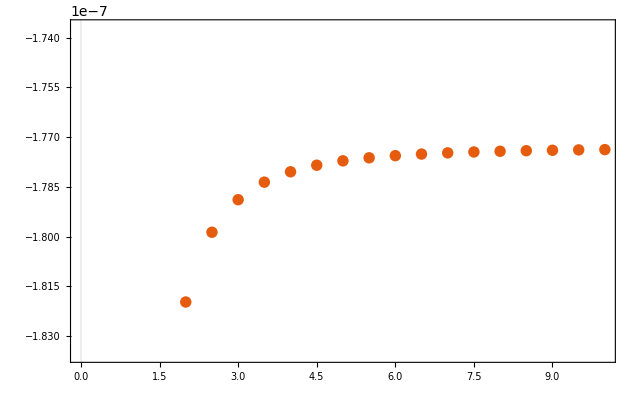

```mathematica
ListPlot[{Extrapolation00}]
```

```mathematica
fitExtrap00=NonlinearModelFit[Extrapolation00[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[-1.80866×10^-7-(3.68164×10^-8)/k^2+(1.47782×10^-8)/k+1.03832×10^-9 Log[k]]

```mathematica
fitExtrap00=NonlinearModelFit[Extrapolation00[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[-1.77719×10^-7-(2.85947×10^-8)/k^2+(5.88903×10^-9)/k]

```mathematica
fitExtrap00["ParameterConfidenceIntervals"]
```

{{-1.77811×10^-7,-1.77627×10^-7},{5.09686×10^-9,6.6812×10^-9},{-2.99892×10^-8,-2.72001×10^-8}}

```mathematica
fit1 =First/@fitExtrap00["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap00["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

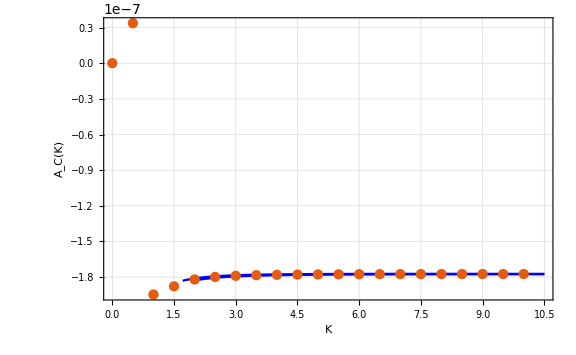

```mathematica
Show[Plot[{fit1,fit2},{k,1,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation00,PlotRange->All],PlotRange->{-1.75*10^-7,-2*10^-7}]
```

### Intertwiners 11

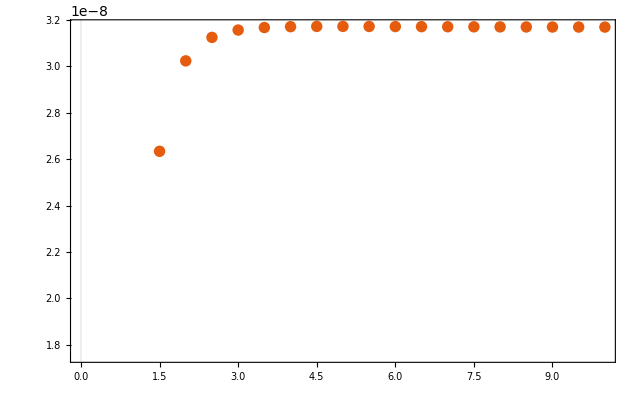

```mathematica
ListPlot[{Extrapolation11}]
```

```mathematica
fitExtrap11=NonlinearModelFit[Extrapolation11[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[2.57253×10^-8-(3.00677×10^-8)/k^2+(2.16008×10^-8)/k+1.7918×10^-9 Log[k]]

```mathematica
fitExtrap11=NonlinearModelFit[Extrapolation11[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[3.11561×10^-8-(1.58797×10^-8)/k^2+(6.26091×10^-9)/k]

```mathematica
fitExtrap11["ParameterConfidenceIntervals"]
```

{{3.09956×10^-8,3.13167×10^-8},{4.88026×10^-9,7.64156×10^-9},{-1.83102×10^-8,-1.34492×10^-8}}

```mathematica
fit1 =First/@fitExtrap11["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap11["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

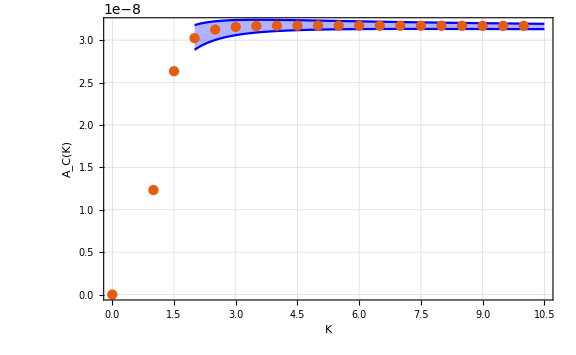

```mathematica
Show[Plot[{fit1,fit2},{k,2,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation11,PlotRange->All],PlotRange->{0,3.2*10^-8}]
```

### Intertwiners 01

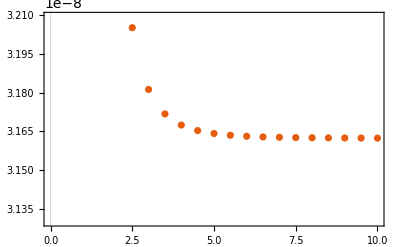

```mathematica
ListPlot[{A01KDl10}]
```

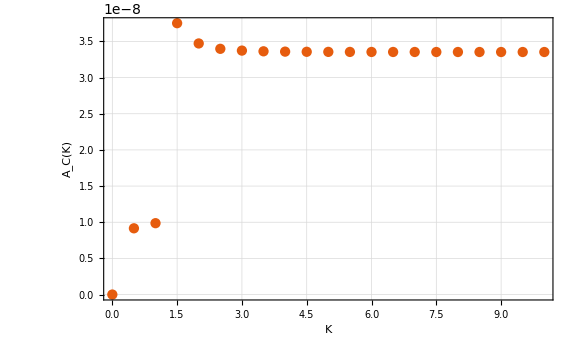

```mathematica
ListPlot[Extrapolation01,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

# Immirzi 1

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_1.0/divergence/cutoff_10.0/goat_Dl_min_0_Dl_max_10.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

{2.86114×10^-14,2.85988×10^-14,-2.93841×10^-13,-2.66425×10^-13,-2.3205×10^-13,-2.10883×10^-13,-1.97077×10^-13,-1.87694×10^-13,-1.81112×10^-13,-1.76369×10^-13,-1.72873×10^-13,-1.70242×10^-13,-1.68228×10^-13,-1.66661×10^-13,-1.65424×10^-13,-1.64436×10^-13,-1.63638×10^-13,-1.62985×10^-13,-1.62447×10^-13,-1.62×10^-13,-1.61625×10^-13}

```mathematica
Extrapolationg1=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1,10,1/2}]&@rExtrapolation]
```

{{0,0},{1,-2.93841×10^-13},{3/2,-2.66425×10^-13},{2,-2.3205×10^-13},{5/2,-2.10883×10^-13},{3,-1.97077×10^-13},{7/2,-1.87694×10^-13},{4,-1.81112×10^-13},{9/2,-1.76369×10^-13},{5,-1.72873×10^-13},{11/2,-1.70242×10^-13},{6,-1.68228×10^-13},{13/2,-1.66661×10^-13},{7,-1.65424×10^-13},{15/2,-1.64436×10^-13},{8,-1.63638×10^-13},{17/2,-1.62985×10^-13},{9,-1.62447×10^-13},{19/2,-1.62×10^-13},{10,-1.61625×10^-13}}

```mathematica
fitExtrapg1=NonlinearModelFit[Extrapolationg1[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[-9.92678×10^-14-(5.70931×10^-14)/k^2-(2.16322×10^-13)/k-1.74868×10^-14 Log[k]]

```mathematica
fitExtrapg1=NonlinearModelFit[Extrapolationg1[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[-1.54045×10^-13-(2.40392×10^-13)/k^2-(4.72292×10^-14)/k]

```mathematica
fitExtrapg1["ParameterConfidenceIntervals"]
```

{{-1.55395×10^-13,-1.52696×10^-13},{-6.03179×10^-14,-3.41405×10^-14},{-2.67748×10^-13,-2.13035×10^-13}}

```mathematica
fit1 =First/@fitExtrapg1["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrapg1["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

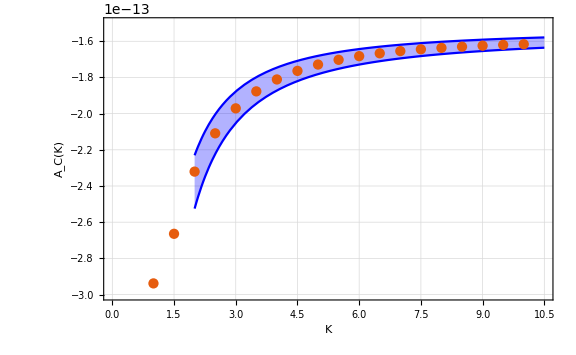

```mathematica
Show[Plot[{fit1,fit2},{k,2,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolationg1,PlotRange->All],PlotRange->{-3*10^-13,-1.5*10^-13}]
```

# Immirzi 0.1 and dimension (2j+1)^2

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_0.1/divergence/cutoff_10.0/goat_Dl_min_0_Dl_max_10_dim_2.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

{3.36679×10^-8,3.37289×10^-8,-2.2224×10^-6,-2.41947×10^-6,-1.9866×10^-6,-1.27157×10^-6,-3.91669×10^-7,5.96989×10^-7,1.65338×10^-6,2.57041×10^-6,4.13276×10^-6,5.31643×10^-6,6.56928×10^-6,7.85699×10^-6,9.17073×10^-6,0.0000105057,0.0000118587,0.0000132273,0.0000146093,0.0000160032,0.0000174076}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation]
```

{{0,0},{1/2,3.37289×10^-8},{1,-2.2224×10^-6},{3/2,-2.41947×10^-6},{2,-1.9866×10^-6},{5/2,-1.27157×10^-6},{3,-3.91669×10^-7},{7/2,5.96989×10^-7},{4,1.65338×10^-6},{9/2,2.57041×10^-6},{5,4.13276×10^-6},{11/2,5.31643×10^-6},{6,6.56928×10^-6},{13/2,7.85699×10^-6},{7,9.17073×10^-6},{15/2,0.0000105057},{8,0.0000118587},{17/2,0.0000132273},{9,0.0000146093},{19/2,0.0000160032},{10,0.0000174076}}

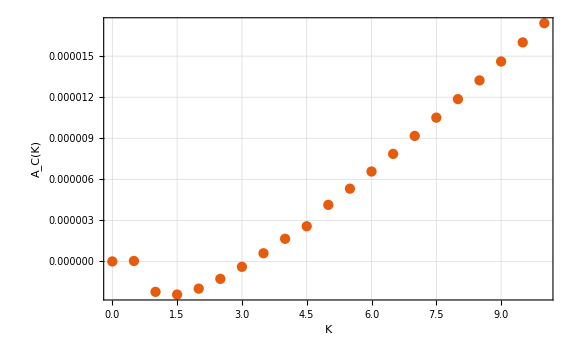

```mathematica
ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],a k^3+ b k^2 + c k+ d,{a,b,c,d},k]
```

FittedModel[-4.13249×10^-6+5.41456×10^-7 k+2.71979×10^-7 k^2-1.11366×10^-8 k^3]

```mathematica
(Normal[fitExtrap]/.Plus->List)/.k->10
```

{-4.13249×10^-6,5.41456×10^-6,0.0000271979,-0.0000111366}

```mathematica
fitExtrap["BestFitParameters"]
```

{a→-1.11366×10^-8,b→2.71979×10^-7,c→5.41456×10^-7,d→-4.13249×10^-6}